```mathematica
<<"Utilities`CleanSlate`";
CleanSlate[];
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 1 Kb

## Spalart, Moser, and Rogers 1991 RK scheme

Scheme (http://dx.doi.org/10.1016/0021-9991(91)90238-G) simplified for one-dimensional diffusive problem represented with a Fourier basis. See notes dated 21 August for the simplification in the context of this model problem.

```mathematica
{Subscript[β, 1],Subscript[β, 2],Subscript[β, 3]}={37/160,5/24,1/6};
{Subscript[γ, 1],Subscript[γ, 2],Subscript[γ, 3]}={8/15,5/12,3/4};
{Subscript[ζ, 0],Subscript[ζ, 1],Subscript[ζ, 2]}={0,-17/60,-5/12};
```

```mathematica
substep[i_]:=((1+(Subscript[β, i]-Subscript[ζ, i-1])z0-Subscript[γ, i] z)Subscript[c, i-1]+Subscript[ζ, i-1](z0-z)Subscript[c, i-2])/(1+Subscript[β, i] z0)
```

```mathematica
substep[1]/.Subscript[c, 0]->1//Simplify
```

(480-256 z+111 z0)/(480+111 z0)

```mathematica
substep[2]/.Subscript[c, 0]->1//Simplify
```

(34 (z-z0)+(120-50 z+59 z0) c_1)/(5 (24+5 z0))

```mathematica
substep[3]/.Subscript[c, 0]->1//Simplify
```

(5 (z-z0) c_1+(12-9 z+7 z0) c_2)/(2 (6+z0))

Combining the three substeps into a single Runge–Kutta time step:

```mathematica
SMR91[νΔtk2_,ν0Δtk2_]:=Module[{z,z0,c1,c2,c3},
(* Notice sign change to match presentation conventions *)
z=-νΔtk2; (*Explicitly treated diffusion *)
z0=-ν0Δtk2; (*Implicitly treated diffusion *)
c1=(480-256 z+111 z0)/(480+111 z0);
c2=(34 (z-z0)+(120-50 z+59 z0) c1)/(5 (24+5 z0));
c3=(5 (z-z0) c1+(12-9 z+7 z0) c2)/(2 (6+z0));
c3
]
```

Does the stability of the explicit portion of the scheme behave as expected?

```mathematica
Explicit[z_]:=SMR91[z,0];
Explicit[z]//FullSimplify
```

1/6 (6+z (6+z (3+z)))

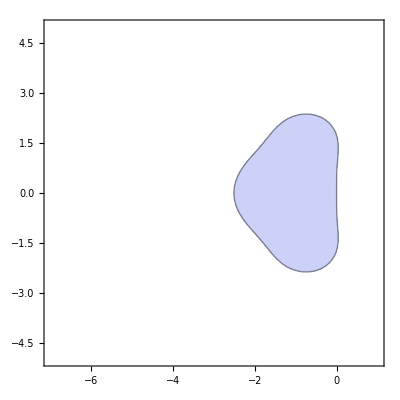

```mathematica
RegionPlot[Abs[Explicit[x+ⅈ y]]≤1,
{x,-7,1},{y,-5,5},Axes->True]
```

Do we recover the expected stability whenever nothing is treated implicitly?

```mathematica
Reduce[Abs[Explicit[x]]==1,x,Reals]
%//N
ExplicitCFL=Abs[Last[Last[%]]]
```

x==0||x==Root[12+6 #1+3 #1^2+#1^3&,1]

x==0.||x==-2.51275

2.51275

Does the stability of the implicit portion of the scheme behave as  expected?

```mathematica
Implicit[z_]:=SMR91[z,z];
Implicit[z]//FullSimplify
```

((6+z) (-40+3 z) (96+29 z))/((-6+z) (-24+5 z) (-160+37 z))

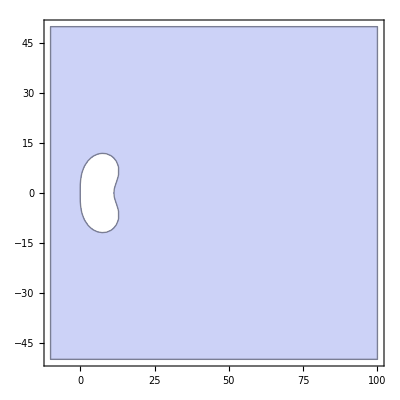

```mathematica
RegionPlot[Abs[Implicit[x+ⅈ y]]≤1,
{x,-10,100},{y,-50,50},Axes->True]
```

```mathematica
Reduce[Abs[Implicit[x]]==1,x,Reals]
%//N
```

x==0||x==Root[-11520+1224 #1-787 #1^2+68 #1^3&,1]

x==0.||x==11.3067

## Linearization about the mean diffusivity

What does the stable region look like when we linearize about a mean diffusivity?
Then the explicitly-treated diffusivity will be at most half of the total diffusivity.

```mathematica
AverageD[z_]:=SMR91[3/2 z,z];
AverageD[z]//FullSimplify
```

-(2 (11520+z (10296+z (3883+962 z))))/((-6+z) (-24+5 z) (-160+37 z))

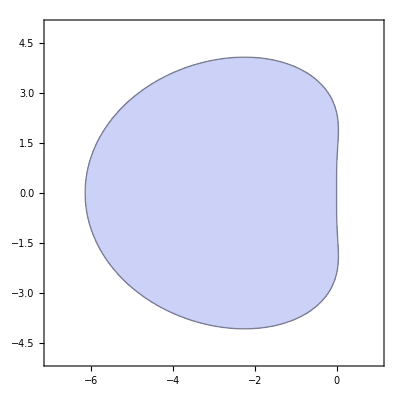

```mathematica
RegionPlot[Abs[AverageD[x+ⅈ y]]≤1,
{x,-7,1},{y,-5,5},Axes->True]
```

```mathematica
Reduce[Abs[AverageD[x]]==1,x,Reals]
%//N
AverageCFL=Abs[Last[Last[%]]]
```

x==0||x==Root[46080+6624 #1+10564 #1^2+1739 #1^3&,1]

x==0.||x==-6.15531

6.15531

As expected, our diffusive stability increased significantly relative to the explicit-only criterion.
The CFL value of 6.15531 would be used in a stability calculation employing the total diffusivity and not the total diffusivity less the reference value. 
This 6.15531 is advantageous compared to using ν-ν_0= 0.5ν with a CFL of 2.51275 giving an "effective CFL" of 5.0255.
The increase in possible time step size is therefore:

```mathematica
AverageCFL/ExplicitCFL
```

2.44963

Equivalently, however, in roughly half the field the explicit term will be antidiffusive with the implicit reference diffusion being sufficiently large to force the combined operator to be diffusive.
We need to investigate any stability restriction stemming from the explicit antidiffusion.

```mathematica
AverageAD[z_]:=SMR91[1/2 z,z];
AverageAD[z]//FullSimplify
```

(960+98 z-34 z^2)/(960-382 z+37 z^2)

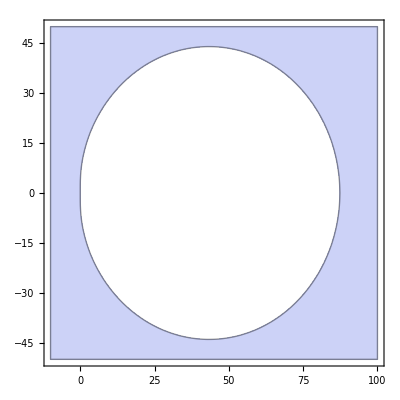

```mathematica
RegionPlot[Abs[AverageAD[x+ⅈ y]]≤1,
{x,-10,100},{y,-50,50},Axes->True]
```

```mathematica
Reduce[Abs[AverageAD[x]]==1,x,Reals]
%//N
```

x==0||x==480/71||x==2/3 (71-√3601)||x==2/3 (71+√3601)

x==0.||x==6.76056||x==7.32778||x==87.3389

```mathematica
x==0.||x==6.76056338028169||x==7.327778163526673||x==87.33888850313998
```

x==0.||x==6.76056||x==7.32778||x==87.3389

From where are the odd roots near x = 7 coming?  Plotting the above along the real axis so that magnitudes of zero correspond to stability boundaries:

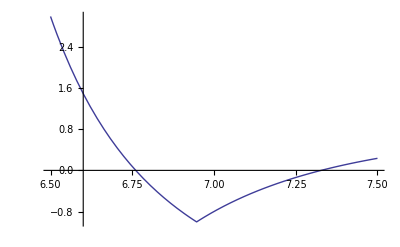

```mathematica
Plot[Abs[AverageAD[x]]-1,{x,6.5,7.5}]
```

Zooming in on this small region within the larger stability map :

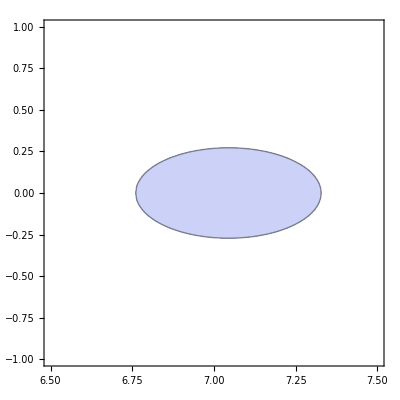

```mathematica
RegionPlot[Abs[AverageAD[x+ⅈ y]]≤1,
{x,6.5,7.5},{y,-1,1},Axes->True]
```

Weird, but irrelevant.

## Linearization about the mean diffusivity (REDUX)

The statement that "the explicitly-treated diffusivity will be at most half of the total diffusivity" depends on the diffusivity being uniformly distributed about the mean.
This may not be true, in practice, and so we should be prepared for diffusivities more than half again as large as the mean.

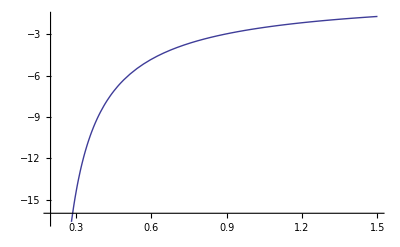

```mathematica
Plot[{
Last[Last[FindRoot[Abs[SMR91[(1+α)x,x]]-1,{x,-AverageCFL},DampingFactor->1/2]]]
},
{α,2/10,3/2}]
redux = Cases[Cases[%,Line[___],Infinity],{_?NumericQ,_?NumericQ},Infinity];
```

We'd like to get a cheap, empirically computable approximation of this shape.
Fit -α^-2 along with constant offsets matching the data at α=0.5 and α=1.0.  Try also with one eyeballed fit non-integer power coefficient.
Included on the plots are the explicit-only diffusive CFL and twice the explicit-only CFL.  These two lines give an indication of the ν-ν_0= 0.5ν stability estimate.

(-2.15531-1/α^2
-1.26253-1/α^2.1
-1.26253-1/α^2)

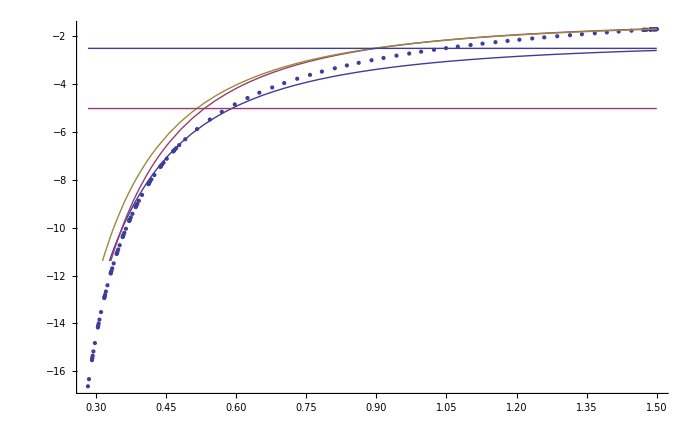

(-2.15531-1/α^2
-1.63895-1/α^2.1
-1.63895-1/α^2)

```mathematica
reduxcurves={
-α^-2-(AverageCFL-(1/2)^-2),
-α^-2.1+(Last[Last[redux]]+First[Last[redux]]^-2),
-α^-2+(Last[Last[redux]]+First[Last[redux]]^-2)
};
Print[MatrixForm[FullSimplify[reduxcurves]]]
Show[
ListPlot[redux],
Plot[reduxcurves,{α,First[First[redux]],First[Last[redux]]}],
Plot[{-ExplicitCFL,-2ExplicitCFL},{α,First[First[redux]],First[Last[redux]]}]
]
```

The latter curve should always be conservative for our cases of interest, but the question is how conservative.
Compute and plot point-by-point relative percent errors for each of the approximations.

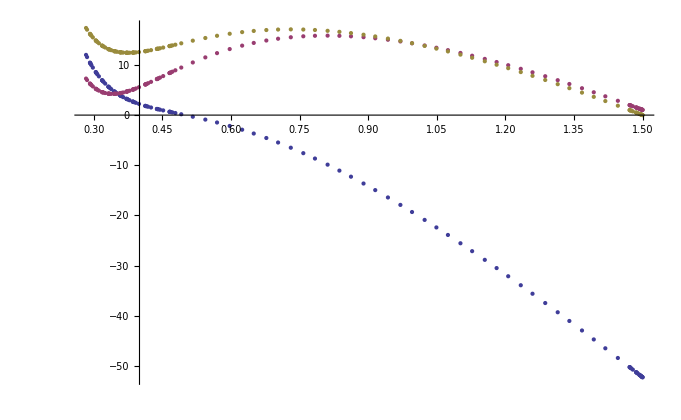

```mathematica
ListPlot[{
{redux⟦All,1⟧,100(Table[reduxcurves⟦1⟧,{α,redux⟦All,1⟧}]-redux⟦All,2⟧)/Abs[redux⟦All,2⟧]}//Transpose,
{redux⟦All,1⟧,100(Table[reduxcurves⟦2⟧,{α,redux⟦All,1⟧}]-redux⟦All,2⟧)/Abs[redux⟦All,2⟧]}//Transpose,
{redux⟦All,1⟧,100(Table[reduxcurves⟦3⟧,{α,redux⟦All,1⟧}]-redux⟦All,2⟧)/Abs[redux⟦All,2⟧]}//Transpose
},PlotRange->Full]
```

In conclusion, if one can pay for the non-integer power, use the second fit.  If one cannot, use the third fit.

## Linearization about the maximum diffusivity

What does the stable region look like when we linearize about the maximum diffusivity?
Then there will be no positive diffusion in the explicit operator but antidiffusion will be present.
Assuming the minimum diffusivity is half the maximum:

```mathematica
MaximumAD[z_]:=SMR91[z,2z];
MaximumAD[z]//FullSimplify
```

(240+(49-34 z) z)/((-3+z) (-80+37 z))

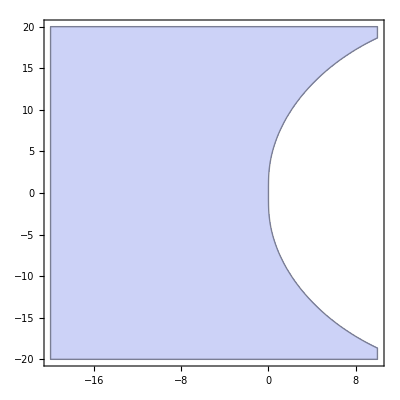

```mathematica
RegionPlot[Abs[MaximumAD[x+ⅈ y]]≤1,
{x,-20,10},{y,-20,20},Axes->True]
```

The above result is for the special case when

ν_max=ν_min+1 ν_min

In general, for some unknown, nonnegative α the situation will be

ν_max=ν_min+αν_min=(1+α)ν_min⇒α=(ν_max-ν_min)/ν_min

```mathematica
AlphaAD[z_,α_]:=SMR91[z,(1+α) z];
AlphaAD[z,α]//FullSimplify
```

(-23040+z (144 (-63+97 α)+z (-350+8372 α-2798 α^2+z (87+α (1055+α (-2687+185 α))))))/((-6+z+z α) (-24+5 z (1+α)) (-160+37 z (1+α)))

Examining a range of α values shows dramatically different behaviors...

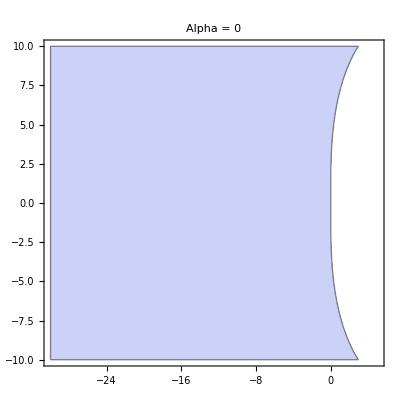

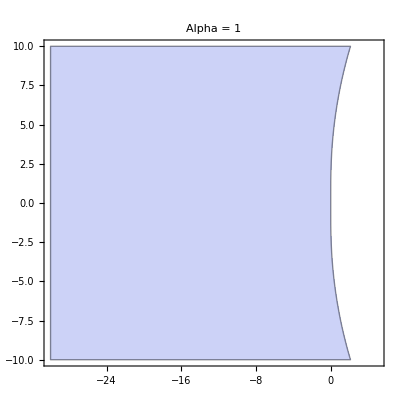

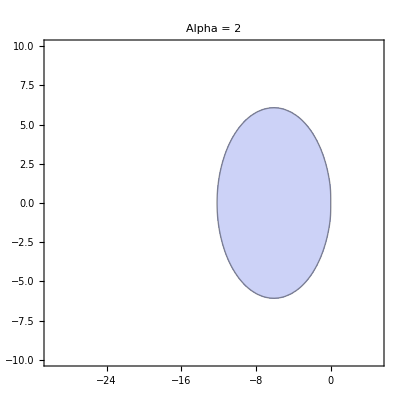

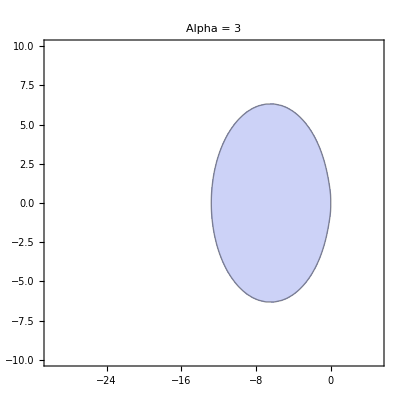

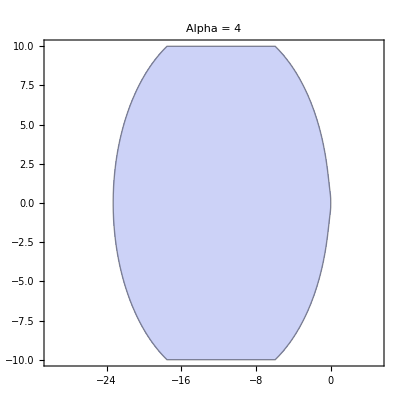

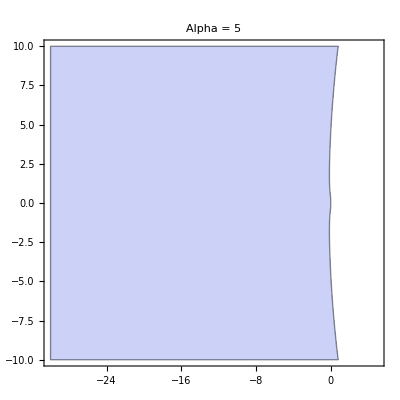

```mathematica
Do[Print[RegionPlot[
Abs[AlphaAD[x+ⅈ y,α]]≤1,
{x,-30,5},{y,-10,10},Axes->True,
PlotLabel->"Alpha = "<>ToString[α]]
],{α,{0,1,2,3,4,5}}]
```

Somewhere between α>0 and α= 4 there may be a unique α giving minimum stability. 
Looking only at the real line and adjusting so that zero crossings indicate stability boundaries:

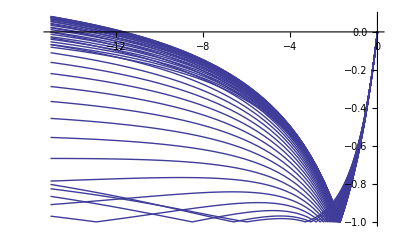

```mathematica
Plot[Table[Abs[AlphaAD[x,α]]-1,{α,0,4,1/10}],{x,-15,0}]
```

There appears to be a limiting effect preventing the stable limit from moving above roughly -11.5 for intermediate α.

Numerically checking the range of α∈[0.75,4.5] shows -11.5 being an acceptable estimate.
The nonsmooth "jumps" to zero indicate where the root search found the x = 0 root instead of what we wanted.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

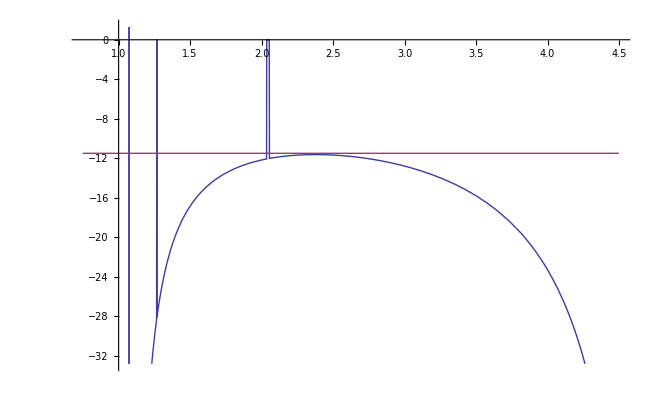

```mathematica
Plot[{
Last[Last[FindRoot[Abs[AlphaAD[x,α]]-1,{x,-100},DampingFactor->1/2]]],
-11.5
},
{α,0.75,4.5}]
```

Examining 0<=α<0.75 (where the above rootfinding approach breaks down) seems to show acceptable behavior:

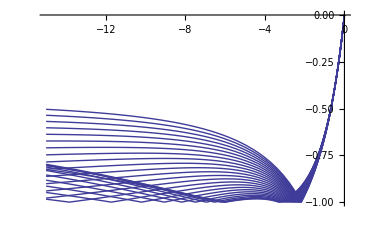

```mathematica
Plot[Table[Abs[AlphaAD[x,α]]-1,{α,0,3/4,1/32}],{x,-15,0}]
```

Examining α>4.5,

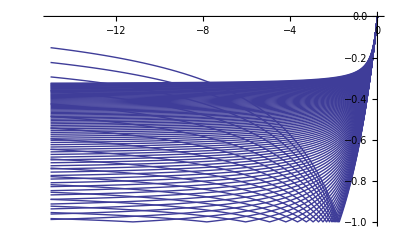

```mathematica
Plot[Table[Abs[AlphaAD[x,α]]-1,{α,4.5,50,0.5}],{x,-15,0}]
```

Empirically, we approximately find 11.5 is available as a stable CFL (to be computed against the total diffusivity) whenever linearization about the maximum diffusivity is performed:

```mathematica
MaximumCFL=11.5;
```

Relative to the purely explicit diffusive timestep, this represents an increase by a factor of

```mathematica
MaximumCFL/ExplicitCFL
```

4.57667

Relative to linearizing about the mean, this is an increase by a factor of

```mathematica
MaximumCFL/AverageCFL
```

1.86831

## Linearization about the minimum diffusivity

The opposite of the previous case would be linearizing about the minimum diffusivity so that the explicit operator is always diffusive.  The same ratio α appears in the analysis.

```mathematica
MinimumD[z_,α_]:=SMR91[(1+α)z, z];
MinimumD[z,α]//FullSimplify
```

-(23040+z (144 (63+160 α)+z (350+144 α (63+80 α)+z (-87+2 α (397+12 α (189+160 α))))))/((-6+z) (-24+5 z) (-160+37 z))

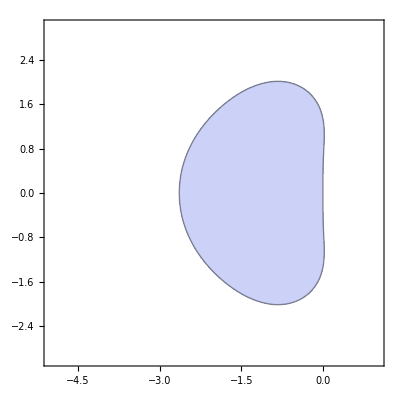

```mathematica
RegionPlot[Abs[MinimumD[x+ⅈ y,1]]≤1,
{x,-5,1},{y,-3,3},Axes->True]
```

This is clearly suboptimal in comparison to the previous two cases and is not investigated further.